## Protein tracing

#### Important things. Only change them if you know what you’re doing

```mathematica
(* Import video and define important parameters *)

SetDirectory[NotebookDirectory[]];
filePath=".\\EGFP_July14\\EGFP_July14_TIFF Files\\Oxyrase\\Low_Conc\\Laser_5\\";
pics=Import[filePath<>"*.tif"]; (* Note file extension here *)

desiredNumberOfProteins=49; 
blinkTraceSmoothing=1; 
maxProteinRadius= 2;
backgroundSubtractionResolution=0.05;
backgroundSubtractionStartingFactor=1;
```

#### Very important code is hidden here ↓↓↓↓ You probably shouldn’t edit or look at the code, but please run it for your protein traces.

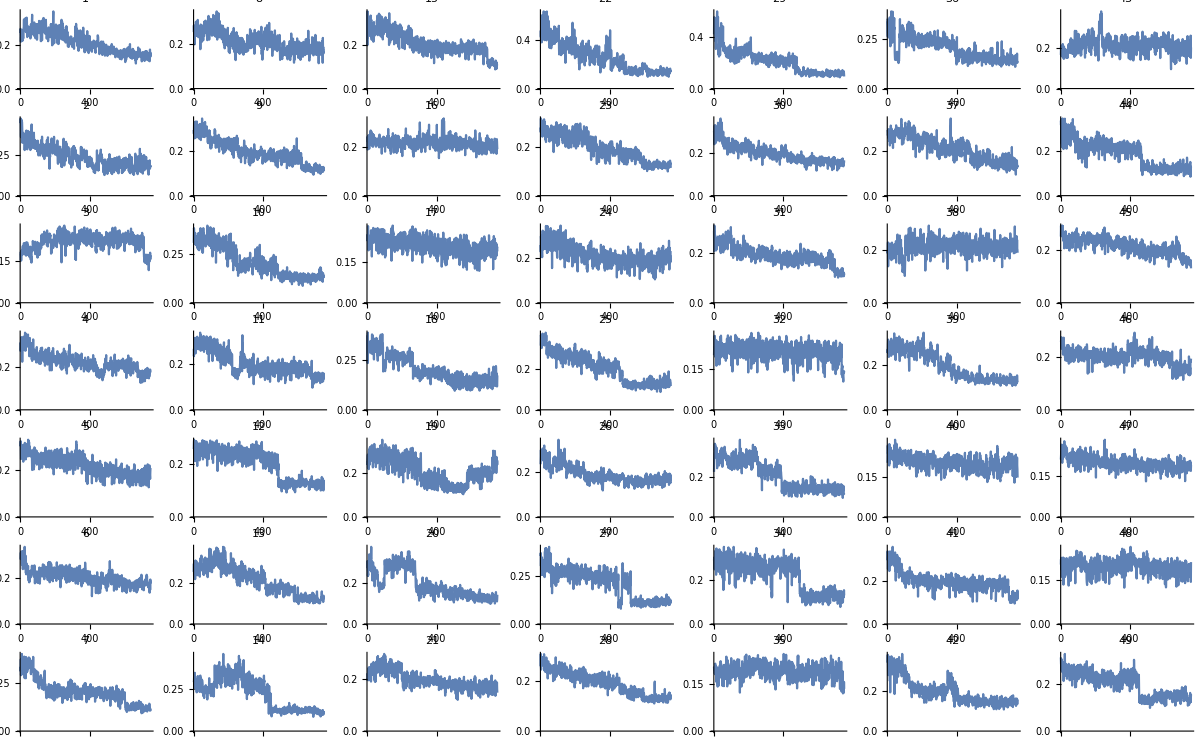

```mathematica
(* ****************************************************************************** *)

(* Defining functions for background subtraction *)
calculateDenoisedData[backgroundImage_]:=(
tempDenoised=rawData-backgroundImage;
tempDenoised=tempDenoised-Min[tempDenoised];
tempDenoised=tempDenoised+1/10 Mean[Flatten[tempDenoised]];
tempDenoised=tempDenoised/Max[tempDenoised];
Return[tempDenoised];
);
picGeometricAvg[pic_]:=Times@@((Times@@pic)^(1/Length[Flatten[pic]]));
picArithmeticAvg[pic_]:=Total[Total[pic]]/Length[Flatten[pic]];
spectralFlatness[pic_]:=picGeometricAvg[pic]/picArithmeticAvg[pic];

(* ****************************************************************************** *)

(* Initial raw data analysis *)

pixelBorderCutoff=1; (* If your heat map image has a weird "dark line" on one of the borders, use this to cut off pixels around the border*)

rawData=Table[Reverse[ImageData[pics[[i]]]],{i,1,Length[pics]}];
rawData=rawData[[All,1+pixelBorderCutoff;;-1-pixelBorderCutoff,1+pixelBorderCutoff;;-1-pixelBorderCutoff]];
rawData=rawData-Min[rawData];
rawData=rawData+1/10 Mean[Flatten[rawData]];
rawData=rawData/Max[rawData];
additive=Total[rawData];

(* ****************************************************************************** *)

(* Fitting gaussian to x-y directions in background *)

ydata=Table[{n,Mean[additive[[n,All]]]},{n,1,Dimensions[additive][[1]]}];
FindFit[ydata,a ⅇ^(-(y-μ)^2/(2 σ^2))+b y,{a,μ,σ,b},y];
yparam={a,μ,σ,b}/.%;
ygauss=Table[{y,yparam[[1]] E^((-(y-yparam[[2]])^2)/(2 yparam[[3]]^2))+yparam[[4]]y},{y,1,Dimensions[additive][[1]]}];
xdata=Table[{n,Mean[additive[[All,n]]]},{n,1,Dimensions[additive][[2]]}];
FindFit[xdata,a ⅇ^(-(x-μ)^2/(2 σ^2))+b x,{a,μ,σ,b},x];
xparam={a,μ,σ,b}/.%;
xgauss=Table[{x,xparam[[1]] E^((-(x-xparam[[2]])^2)/(2 xparam[[3]]^2))+xparam[[4]]x},{x,1,Dimensions[additive][[2]]}];
background=Transpose[Table[1/(√(xparam[[1]]yparam[[1]]))(xparam[[1]] E^((-(x-xparam[[2]])^2)/(2 xparam[[3]]^2))+xparam[[4]]x)(yparam[[1]] E^((-(y-yparam[[2]])^2)/(2 yparam[[3]]^2))+yparam[[4]]y),{x,1,Dimensions[additive][[2]]},{y,1,Dimensions[additive][[1]]}]];
background=Table[background,{i,1,Length[rawData]}];

(* ****************************************************************************** *)

(* Optimizing background subtraction factor. Optimizes for signal "flatness" *)

ϵ=backgroundSubtractionStartingFactor;
previousSpectralFlatness=spectralFlatness[additive];
flatnessVariation={};
flatnessVariationPics={};

deNoised=calculateDenoisedData[ϵ/Length[rawData]*background];
deNoisedAdd=Total[deNoised];

deNoisedSpectralFlatness=spectralFlatness[deNoisedAdd];
AppendTo[flatnessVariation,{ϵ,deNoisedSpectralFlatness}];

While[deNoisedSpectralFlatness>previousSpectralFlatness,
previousSpectralFlatness=deNoisedSpectralFlatness;
AppendTo[flatnessVariationPics,deNoisedAdd];

ϵ=ϵ+backgroundSubtractionResolution;
deNoised=calculateDenoisedData[ϵ/Length[rawData]*background];
deNoisedAdd=Total[deNoised];

deNoisedSpectralFlatness=spectralFlatness[deNoisedAdd];
AppendTo[flatnessVariation,{ϵ,deNoisedSpectralFlatness}];
];
BSMF=ϵ=ϵ-backgroundSubtractionResolution;
deNoisedAdd=flatnessVariationPics[[-1]];

(* ****************************************************************************** *)

(* Time-dependent background subtraction factor. Bi-exponential fit and subtracting fast component *)

tempAnalysisArray=deNoised;
timeAvgBrightness=Table[Mean[Flatten[tempAnalysisArray[[ii]]]],{ii,Length[deNoised]}];
exponentialFit=FindFit[timeAvgBrightness,{a1 ⅇ^((- t)/τ1)+a2 ⅇ^((- t)/τ2)+b,{a1>0, b>0, τ2>τ1>1,a2>0}},{a1, τ1,a2, τ2,b},t];
timeParam={a1, τ1,a2, τ2,b}/.exponentialFit;
timeFit1=Table[timeParam[[1]] ⅇ^((- t)/timeParam[[2]])+timeParam[[5]],{t,1,Length[timeAvgBrightness]}];
timeFit2=Table[timeParam[[3]] ⅇ^((- t)/timeParam[[4]])+timeParam[[5]],{t,1,Length[timeAvgBrightness]}];
timeDecayFit=Table[timeParam[[1]] ⅇ^((- t)/timeParam[[2]])+timeParam[[3]] ⅇ^((- t)/timeParam[[4]])+timeParam[[5]],{t,1,Length[timeAvgBrightness]}];

avgBackground=Mean[Mean[background[[1]]]];
backgroundTD=Table[(timeFit1[[i]]/avgBackground)background[[i]],{i,Length[background]}]; (* Change how many exponentials you want here by changing "timeFit1" array to "timeFit2" or "timeDecayFit" *)
deNoisedTD=calculateDenoisedData[backgroundTD];

tempAnalysisArray=deNoisedTD;
timeAvgBrightness=Table[Mean[Flatten[tempAnalysisArray[[ii]]]],{ii,Length[tempAnalysisArray]}];

(* ****************************************************************************** *)

(* 2nd optimizing background subtraction factor. Optimizes for signal "flatness" *)

ϵ=backgroundSubtractionStartingFactor;
previousSpectralFlatness=spectralFlatness[additive];
flatnessVariation={};
flatnessVariationPics={};

deNoisedTD=calculateDenoisedData[ϵ/Length[rawData]*backgroundTD];
deNoisedTDAdd=Total[deNoisedTD];

deNoisedSpectralFlatness=spectralFlatness[deNoisedTDAdd];
AppendTo[flatnessVariation,{ϵ,deNoisedSpectralFlatness}];

While[deNoisedSpectralFlatness>previousSpectralFlatness,
previousSpectralFlatness=deNoisedSpectralFlatness;
AppendTo[flatnessVariationPics,deNoisedTDAdd];

ϵ=ϵ+10^3 backgroundSubtractionResolution;
deNoisedTD=calculateDenoisedData[ϵ/Length[rawData]*backgroundTD];
deNoisedTDAdd=Total[deNoisedTD];

deNoisedSpectralFlatness=spectralFlatness[deNoisedTDAdd];
AppendTo[flatnessVariation,{ϵ,deNoisedSpectralFlatness}];
];
BSMF=ϵ=ϵ-backgroundSubtractionResolution;
deNoisedTDAdd=flatnessVariationPics[[-1]];

(* ****************************************************************************** *)

(* Protein searching *)

analysisArray=deNoisedTD; 
brightnessThreshold=Mean[Flatten[Total[analysisArray]]]+StandardDeviation[Flatten[Total[analysisArray]]];


tempAnalysisArray=Total[analysisArray];
width=maxProteinRadius-1;
proteins={};
(* Keep going until it finds the proper number of traces *)
For[iterator=0,iterator<desiredNumberOfProteins,iterator++,
i=j=1;

(* Iterate over x to find location of maximum *)
While[i≤Length[tempAnalysisArray]&&iterator<desiredNumberOfProteins,
j=1;
(* Iterate over y to find location of maximum *)
While[j≤Length[tempAnalysisArray[[i]]]&&iterator<desiredNumberOfProteins,

(* Once you find maximum value, do this *)
If[tempAnalysisArray[[i,j]]==Max[tempAnalysisArray],

(* Append location of maximum value and begin scan of (2*width + 1)^2 pixel grid centered at maximum value *)
AppendTo[proteins,{}];
For[ip=Max[i-width,1],ip≤Min[i+width,Length[tempAnalysisArray]],ip++,
For[jp=Max[j-width,1],jp≤Min[j+width,Length[tempAnalysisArray[[ip]]]],jp++,

If[tempAnalysisArray[[ip,jp]]>brightnessThreshold,
AppendTo[proteins[[Length[proteins]]],{ip,jp}];
];

tempAnalysisArray[[ip,jp]]=0;
];
];
i=Length[tempAnalysisArray];
j=Length[tempAnalysisArray[[i]]];
];
j++;
];
i++;
];
];
ClearAll[i,j,ip,jp,iterator];

blink={};
For[prot=1,prot≤desiredNumberOfProteins,prot++,
AppendTo[blink,Table[
{t,Mean[
Table[
analysisArray[[    t    ]][[     proteins[[prot,i,1]]    ]][[    proteins[[prot,i,2]]    ]],
{i,Length[proteins[[prot]]]}
]
]}
,{t,1,Length[analysisArray]}]];
];
ClearAll[prot];

graphicsGridSize=Ceiling[√desiredNumberOfProteins];
plots=Table[{},{ii,graphicsGridSize}];
trace=1;
While[trace≤desiredNumberOfProteins,
index=Mod[trace,graphicsGridSize];
If[index==0,index=graphicsGridSize];
AppendTo[plots[[index]],ListLinePlot[Mean[Transpose[Partition[blink[[trace]],blinkTraceSmoothing]]],PlotRange->All,PlotLabel->ToString[trace]]];
trace++;
];
GraphicsGrid[plots,ImageSize->1200]
```

## Exporting videos

### Exports blink traces for use in origin

```mathematica
SetDirectory[NotebookDirectory[]];
fileName="EnterFileNameHereWithoutFileExtension"
exportData=Table[i,{i,1,Length[blink[[1]]]},{j,1,Length[blink]-1}];
For[ii=1,ii≤Length[blink]-2,ii++,
For[jj=1,jj≤Length[blink[[ii]]],jj++,
exportData[[jj,ii+1]]=blink[[ii,jj,2]];
];
];
Export[fileName<>".csv",exportData];
```

### Renders and exports the video

```mathematica
SetDirectory[NotebookDirectory[]];
fileNameRoot="EnterFileNameHereWithoutFileExtension";

(* Exports original video as gif *)
ogVid=Table[Image[rawData[[u]],ImageSize->600],{u,Length[rawData]}];
Export[fileNameRoot<>".gif",ogVid];
ListAnimate[ogVid,ImageSize->600]

(* Exports gaussian-background-subtracted video as gif *)
gaussSubVid=Table[Image[deNoised[[u]],ImageSize->600],{u,Length[deNoised]}];
Export[fileNameRoot<>"_GaussianSub.gif",gaussSubVid];
ListAnimate[gaussSubVid,ImageSize->600]

(* Exports gaussian-background-subtracted and time-dependence-subtracted video as gif *)
TDSubVid=Table[Image[deNoisedTD[[u]],ImageSize->600],{u,Length[deNoisedTD]}];
Export[fileNameRoot<>"_TDGaussianSub.gif",TDSubVid];
ListAnimate[TDSubVid,ImageSize->600]
```